## Primordial Black Holes Generated by Fast-roll Mechanism in Noncanonical Natural Inflation

Soma Heydari and Kayoomars Karami

ApJ  975 148 (2024)

## Fitting Ω_GW A&D

```mathematica
SetDirectory[NotebookDirectory[]];
oa=Import["GWA.dat"];
```

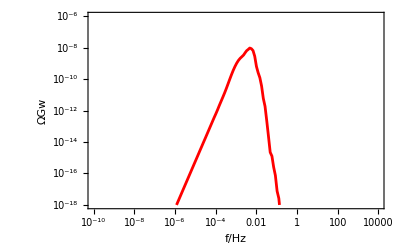

```mathematica
omega=ListLogLogPlot[{oa},Frame->True,PlotRange->{{10^-10,10^4},{10^-18,10^-6}},PlotStyle->{Red},FrameLabel->{"f/Hz","ΩGw"},RotateLabel->False,Joined->True,Axes->False,LabelStyle->{FontFamily->"Cambria",Bold,GrayLevel[0]}]
```

```mathematica
oa
```

{{5.23482×10^-9,8.54057×10^-26},{6.37965×10^-9,1.54586×10^-25},{7.77476×10^-9,2.79796×10^-25},{9.47487×10^-9,5.06408×10^-25},{1.15466×10^-8,9.16525×10^-25},{1.40712×10^-8,1.65873×10^-24},{1.71477×10^-8,3.00189×10^-24},{2.08965×10^-8,5.43252×10^-24},{2.54646×10^-8,9.83077×10^-24},{3.1031×10^-8,1.77895×10^-23},{3.78137×10^-8,3.21904×10^-23},{4.60786×10^-8,5.82474×10^-23},{5.61493×10^-8,1.05394×10^-22},{6.84202×10^-8,1.90692×10^-22},{8.33718×10^-8,3.45022×10^-22},{1.0159×10^-7,6.2419×10^-22},{1.23787×10^-7,1.12931×10^-21},{1.50833×10^-7,2.04304×10^-21},{1.83785×10^-7,3.69596×10^-21},{2.23935×10^-7,6.68576×10^-21},{2.72851×10^-7,1.20942×10^-20},{3.3245×10^-7,2.18757×10^-20},{4.05061×10^-7,3.95653×10^-20},{4.93526×10^-7,7.15696×10^-20},{6.01304×10^-7,1.2944×10^-19},{7.3261×10^-7,2.34109×10^-19},{8.92578×10^-7,4.23359×10^-19},{1.08746×10^-6,7.65739×10^-19},{1.32488×10^-6,1.3846×10^-18},{1.61411×10^-6,2.50379×10^-18},{1.96645×10^-6,4.52806×10^-18},{2.39568×10^-6,8.18879×10^-18},{2.91855×10^-6,1.47926×10^-17},{3.5555×10^-6,2.67614×10^-17},{4.33139×10^-6,4.83681×10^-17},{5.27653×10^-6,8.75056×10^-17},{6.42781×10^-6,1.58063×10^-16},{7.83019×10^-6,2.86167×10^-16},{9.5384×10^-6,5.17181×10^-16},{0.0000116191,9.3312×10^-16},{0.0000141535,1.68716×10^-15},{0.0000172404,3.06599×10^-15},{0.0000210003,5.515×10^-15},{0.0000255797,9.98934×10^-15},{0.0000311572,1.79321×10^-14},{0.0000379503,3.24791×10^-14},{0.0000462236,5.88798×10^-14},{0.0000562996,1.06559×10^-13},{0.0000685705,1.92925×10^-13},{0.0000835144,3.48627×10^-13},{0.000101713,6.14078×10^-13},{0.000123875,1.11271×10^-12},{0.000150862,2.08885×10^-12},{0.000183724,3.8006×10^-12},{0.000223738,6.92121×10^-12},{0.000272458,1.27657×10^-11},{0.000331775,2.44313×10^-11},{0.000403987,4.8498×10^-11},{0.000491894,9.65322×10^-11},{0.000598891,1.88875×10^-10},{0.000729104,3.55661×10^-10},{0.000887531,6.23976×10^-10},{0.00108023,1.01874×10^-9},{0.00131452,1.52658×10^-9},{0.00159913,2.07671×10^-9},{0.00194442,2.63651×10^-9},{0.00236207,3.36949×10^-9},{0.00286082,4.8518×10^-9},{0.00335756,6.38515×10^-9},{0.00396863,7.56876×10^-9},{0.00474046,9.37121×10^-9},{0.0057018,8.51823×10^-9},{0.00688763,6.43296×10^-9},{0.00834185,2.80901×10^-9},{0.0101187,6.35084×10^-10},{0.0122856,2.53175×10^-10},{0.0149252,1.21391×10^-10},{0.0181376,3.60553×10^-11},{0.0220455,5.91028×10^-12},{0.0267984,1.85334×10^-12},{0.0325777,2.19642×10^-13},{0.0396044,2.26529×10^-14},{0.0481467,2.21332×10^-15},{0.0585308,1.26824×10^-15},{0.0711527,2.52817×10^-16},{0.0864939,7.50028×10^-17},{0.105139,7.60939×10^-18},{0.127798,2.62433×10^-18},{0.155335,2.11457×10^-19},{0.188796,2.24447×10^-20},{0.229454,6.73535×10^-21},{0.278854,1.07224×10^-21},{0.338874,3.41651×10^-23},{0.411792,7.06739×10^-24},{0.500376,3.14746×10^-24},{0.607982,1.4051×10^-24},{0.738691,6.22204×10^-25},{0.897449,2.82818×10^-25},{1.09026,1.2741×10^-25}}

```mathematica
ScientificForm[0.004740459037830107]
(*peak={0.004740459037830107,9.371210988537963*^-9};*)
```

4.74046×10^-3

```mathematica
fc1=0.004740459037830107;
```

```mathematica
data3={{1.614107818301057*^-6,2.5037875079043124*^-18},{1.966451535158584*^-6,4.528057976803173*^-18},{2.395676329291396*^-6,8.188787115236366*^-18},{2.9185501623568717*^-6,1.479255185392521*^-17},{3.5554964154252765*^-6,2.6761393001861917*^-17},{4.33139037427988*^-6,4.836808403052412*^-17},{5.276529170411107*^-6,8.750564705976813*^-17},{6.427812931038829*^-6,1.580627844994122*^-16},{7.830187407492793*^-6,2.8616703392528757*^-16},{9.53839660158806*^-6,5.171813347329118*^-16},{0.00001161909385782658,9.331195739160903*^-16},{0.000014153466162053545,1.6871566780752746*^-15},{0.00001724039237912465,3.0659875885725944*^-15},{0.000021000263725484975,5.515001529315971*^-15},{0.000025579697455910974,9.989339948404957*^-15}};
```

```mathematica
CC=FindFit[data3, .02 x^(d-2/Log[fc1/x]),{d,b},x]
```

{d→3.05883,b→1.}

```mathematica
ddC=CC[[1]][[2]]
bbC=CC[[2]][[2]]
```

3.05883

1.

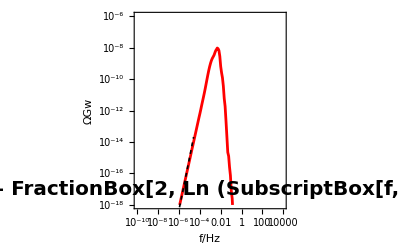

```mathematica
fitA=LogLogPlot[{.04 x^(d-b/Log[fc1/x])/.{d->ddC,b->2}},{x,data3[[1,1]]*.5,data3[[Length[data3],1]]*1},PlotStyle->{{Dashing[0.007],Black,Thickness[0.003]}}];
Show[omega,fitA,Epilog->{Text[Style["f^(3 - FractionBox[2, Ln (SubscriptBox[f, c]/f)])",20,FontFamily->"Cambria",Bold],Scaled[{0.47,0.1}]]}]
```

```mathematica
data={{0.000056299560939662806,1.0655881238728356*^-13},{0.00006857054362517175,1.9292531545442428*^-13},{0.00008351443103981623,3.486267810464713*^-13},{0.00010171302015639825,6.140780035051243*^-13},{0.00012387474921268042,1.1127092800568283*^-12},{0.00015086195401186136,2.0888504716258138*^-12},{0.00018372381771517506,3.8006032900194416*^-12},{0.00022373778614478323,6.921212997974128*^-12},{0.0002724578404559919,1.2765748829692697*^-11},{0.00033177454268866463,2.4431295408825563*^-11},{0.00040398735565792956,4.84980320602629*^-11},{0.0004918937466227576,9.65322439100725*^-11},{0.0005988913213492409,1.8887513357649872*^-10},{0.0007291039040558738,3.5566073190313847*^-10},{0.0008875310150342972,6.239755631270965*^-10},{0.001080234627047522,1.0187441646374569*^-9},{0.0013145224883964472,1.5265753167427881*^-9},{0.0015991327306590297,2.0767059724198495*^-9},{0.0019444203700769893,2.6365071344143542*^-9},{0.002362074207945026,3.3694865868632774*^-9},{0.002860824049050753,4.851801843272338*^-9},{0.003357561723709423,6.385147365210256*^-9}};
```

```mathematica
AA=FindFit[data,s x^b,{s,b},x]
```

{s→0.0000857559,b→1.66897}

```mathematica
{b,s}/.AA
```

{1.66897,0.0000857559}

```mathematica
ddA=AA[[1]][[2]]
bbA=AA[[2]][[2]]
```

0.0000857559

1.66897

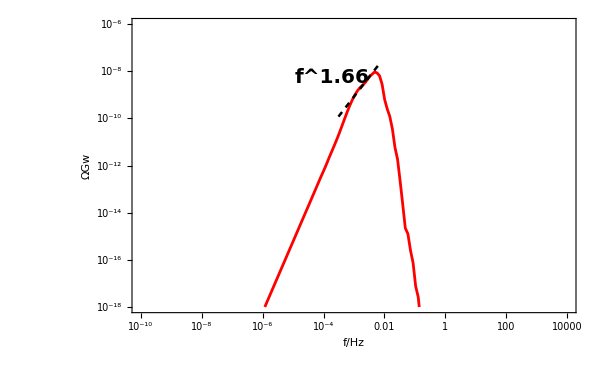

```mathematica
fitB=Show[LogLogPlot[s x^b/.{s->ddA,b->bbA},{x,data[[1,1]]*5.5,data[[Length[data],1]]*2},PlotStyle->{{Dashing[0.007],Black,Thickness[0.003]}}]];
Show[omega,fitB,Epilog->{Text[Style["f^1.66",20,FontFamily->"Cambria",Bold],Scaled[{0.45,.8}]]},ImageSize->{600,400}]
```

```mathematica
data2={{0.006887632911598906,6.432956055911077*^-9},{0.008341849460468554,2.809005306790082*^-9},{0.010118674938018659,6.350836491630752*^-10},{0.012285589673123556,2.531746992741354*^-10},{0.01492521196036421,1.213910821740405*^-10},{0.018137617878569153,3.6055262270693176*^-11},{0.022045540894378966,5.910283092198951*^-12},{0.02679835719367117,1.853341591764455*^-12},{0.03257769567170263,2.1964162549345654*^-13},{0.039604363246106306,2.2652899424794935*^-14},{0.048146707101692866,2.2133192834559684*^-15},{0.05853077155785906,1.2682392348665774*^-15},{0.0711527195825414,2.528173829652042*^-16}};
```

```mathematica
BB=FindFit[data2,d x^-b,{d,b},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{d→3.55938×10^-19,b→4.7412}

```mathematica
ddB=BB[[1]][[2]];
bbB=BB[[2]][[2]];
```

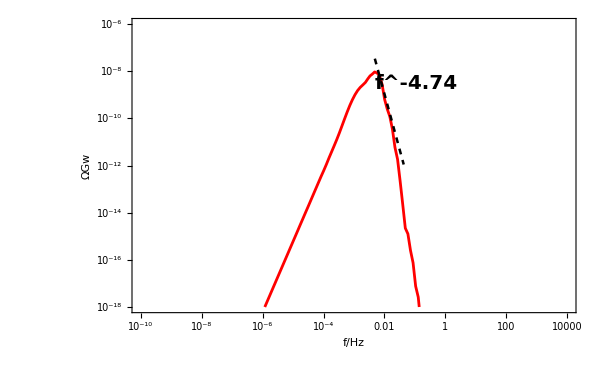

```mathematica
fitC=LogLogPlot[d x^-b/.{d->ddB,b->bbB},{x,data2[[1,1]]*0.7,data2[[Length[data2],1]]*.6},PlotStyle->{{Dashing[0.007],Black,Thickness[0.003]}}];
Show[omega,fitC,Epilog->{
Text[Style["f^-4.74",20,FontFamily->"Cambria",Bold],Scaled[{0.64,.78}]]},ImageSize->{600,400}]
```

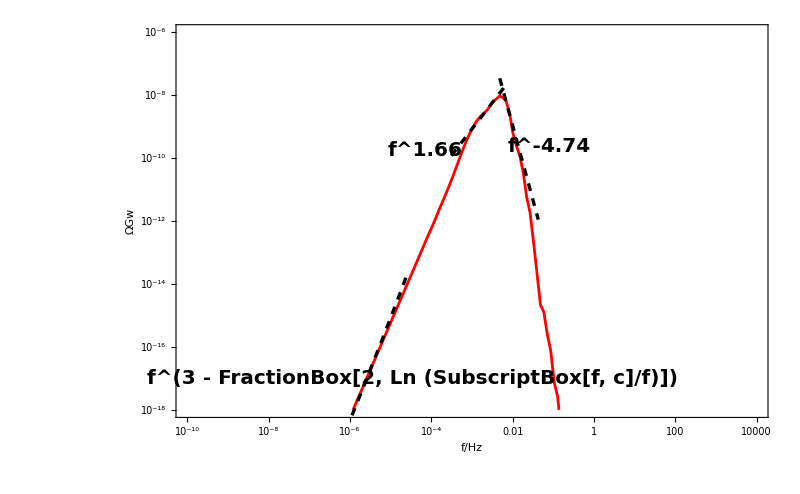

```mathematica
Show[omega,fitC,fitB,fitA,Epilog->{Text[Style["f^(3 - FractionBox[2, Ln (SubscriptBox[f, c]/f)])",20,FontFamily->"Cambria",Bold],Scaled[{0.40,0.1}]],Text[Style["f^1.66",20,FontFamily->"Cambria",Bold],Scaled[{0.42,.68}]],
Text[Style["f^-4.74",20,FontFamily->"Cambria",Bold],Scaled[{0.63,.69}]]},ImageSize->{800,600}]
```

### Fitting Ω_GW D

```mathematica
SetDirectory[NotebookDirectory[]];
od=Import["GWD.dat"];
```

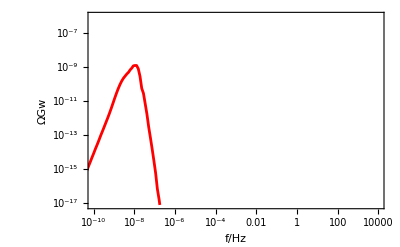

```mathematica
omega=ListLogLogPlot[{od},Frame->True,PlotRange->{{10^-10,10^4},{8*10^-18,10^-6}},PlotStyle->{Red},FrameLabel->{"f/Hz","ΩGw"},RotateLabel->False,Joined->True,Axes->False,LabelStyle->{FontFamily->"Cambria",Bold,GrayLevel[0]}]
```

```mathematica
od
```

{{4.98309×10^-15,1.05771×10^-27},{6.07619×10^-15,1.91761×10^-27},{7.40902×10^-15,3.47657×10^-27},{9.03416×10^-15,6.30278×10^-27},{1.10157×10^-14,1.14263×10^-26},{1.34318×10^-14,2.07144×10^-26},{1.63778×10^-14,3.75519×10^-26},{1.99697×10^-14,6.80744×10^-26},{2.43493×10^-14,1.23404×10^-25},{2.96892×10^-14,2.23698×10^-25},{3.61999×10^-14,4.05499×10^-25},{4.41382×10^-14,7.35037×10^-25},{5.38168×10^-14,1.33237×10^-24},{6.56175×10^-14,2.41506×10^-24},{8.00052×10^-14,4.37749×10^-24},{9.75471×10^-14,7.93442×10^-24},{1.18934×10^-13,1.43811×10^-23},{1.4501×10^-13,2.60651×10^-23},{1.76801×10^-13,4.72417×10^-23},{2.15561×10^-13,8.56233×10^-23},{2.62817×10^-13,1.55176×10^-22},{3.20429×10^-13,2.81225×10^-22},{3.90669×10^-13,5.09678×10^-22},{4.76302×10^-13,9.23684×10^-22},{5.80701×10^-13,1.67383×10^-21},{7.0798×10^-13,3.0336×10^-21},{8.63148×10^-13,5.49728×10^-21},{1.05232×10^-12,9.96131×10^-21},{1.28294×10^-12,1.80521×10^-20},{1.56409×10^-12,3.27072×10^-20},{1.90684×10^-12,5.92617×10^-20},{2.32469×10^-12,1.07385×10^-19},{2.83407×10^-12,1.94557×10^-19},{3.45505×10^-12,3.52502×10^-19},{4.21206×10^-12,6.38946×10^-19},{5.13489×10^-12,1.15735×10^-18},{6.25987×10^-12,2.09666×10^-18},{7.63125×10^-12,3.79936×10^-18},{9.30299×10^-12,6.87618×10^-18},{1.13409×10^-11,1.24638×10^-17},{1.38251×10^-11,2.25939×10^-17},{1.68533×10^-11,4.08594×10^-17},{2.05446×10^-11,7.42121×10^-17},{2.50442×10^-11,1.34513×10^-16},{3.05291×10^-11,2.43746×10^-16},{3.72148×10^-11,4.39589×10^-16},{4.53644×10^-11,7.98054×10^-16},{5.5298×10^-11,1.47289×10^-15},{6.74063×10^-11,2.63565×10^-15},{8.21651×10^-11,4.83443×10^-15},{1.00154×10^-10,8.67621×10^-15},{1.22081×10^-10,1.59692×10^-14},{1.48806×10^-10,2.81844×10^-14},{1.81379×10^-10,5.12408×10^-14},{2.21079×10^-10,9.55707×10^-14},{2.69464×10^-10,1.70767×10^-13},{3.28434×10^-10,3.09346×10^-13},{4.003×10^-10,5.64999×10^-13},{4.87881×10^-10,1.02707×10^-12},{5.94611×10^-10,1.91832×10^-12},{7.24668×10^-10,3.71565×10^-12},{8.83134×10^-10,7.3983×10^-12},{1.0762×10^-9,1.47936×10^-11},{1.3114×10^-9,2.88463×10^-11},{1.59789×10^-9,5.3514×10^-11},{1.94678×10^-9,9.31397×10^-11},{2.37153×10^-9,1.50419×10^-10},{2.88842×10^-9,2.22492×10^-10},{3.51696×10^-9,2.99345×10^-10},{4.28029×10^-9,3.99666×10^-10},{5.20437×10^-9,5.05735×10^-10},{6.29124×10^-9,7.0817×10^-10},{7.4386×10^-9,8.71485×10^-10},{8.87786×10^-9,1.19256×10^-9},{1.06758×10^-8,1.25681×10^-9},{1.29008×10^-8,1.25239×10^-9},{1.56366×10^-8,8.04723×10^-10},{1.89871×10^-8,2.88434×10^-10},{2.30813×10^-8,5.69917×10^-11},{2.80769×10^-8,2.8777×10^-11},{3.41678×10^-8,7.11491×10^-12},{4.15908×10^-8,1.7371×10^-12},{5.06342×10^-8,3.09879×10^-13},{6.16499×10^-8,7.18086×10^-14},{7.50668×10^-8,1.5728×10^-14},{9.1407×10^-8,3.19959×10^-15},{1.11306×10^-7,6.00272×10^-16},{1.3554×10^-7,6.96401×10^-17},{1.65049×10^-7,1.65981×10^-17},{2.00984×10^-7,2.93722×10^-18},{2.44741×10^-7,2.97209×10^-19},{2.98022×10^-7,4.76071×10^-20},{3.62898×10^-7,6.91364×10^-21},{4.4189×10^-7,7.40516×10^-22},{5.38068×10^-7,3.00787×10^-23}}

```mathematica
ScientificForm[1.0675806103846157*^-8]
(*peak={1.0675806103846157*^-8,1.2568143538904348*^-9};*)
```

1.06758×10^-8

```mathematica
fc1=1.0675806103846157*^-8;
```

```mathematica
data3={{1.1340874906309083*^-11,1.2463786533741779*^-17},{1.3825057347097043*^-11,2.259392976574632*^-17},{1.685325860640866*^-11,4.08594459725887*^-17},{2.0544582397922177*^-11,7.421212340443321*^-17},{2.504420152262191*^-11,1.3451340508907228*^-16},{3.052906125103151*^-11,2.4374638215854203*^-16},{3.7214830795057606*^-11,4.395891464964475*^-16},{4.5364368011173175*^-11,7.980540593426667*^-16},{5.529804338691703*^-11,1.4728872709397923*^-15},{6.740632673181055*^-11,2.6356487198983083*^-15},{8.216510880605967*^-11,4.83443276489987*^-15},{1.0015430356922341*^-10,8.676214386447175*^-15},{1.2208066693015309*^-10,1.5969200565660502*^-14},{1.4880552861087*^-10,2.8184369571808416*^-14},{1.8137857207345413*^-10,5.124079597469412*^-14},{2.2107880871654971*^-10,9.55707381715364*^-14},{2.6946437543892475*^-10,1.7076728228243801*^-13},{3.284336668629635*^-10,3.0934556336556954*^-13},{4.002999364266545*^-10,5.64998562494407*^-13},{4.878814286546228*^-10,1.0270682772030867*^-12},{5.946106781476516*^-10,1.918322708558363*^-12},{7.246676746162191*^-10,3.71565215648251*^-12},{8.831335898129365*^-10,7.398296845518312*^-12},{1.0762005770936058*^-9,1.4793574965712126*^-11},{1.3113989642046978*^-9,2.8846346891204456*^-11},{2.371530301910455*^-9,1.5041860018002444*^-10},{2.8884166828965023*^-9,2.2249189877310605*^-10},{3.5169644460044562*^-9,2.9934465686392643*^-10},{4.280291080422795*^-9,3.99666049495257*^-10}};
```

```mathematica
CC=FindFit[data3,.01 x^(d-2/Log[fc1/x]),{d,b},x]
```

{d→3.07233,b→1.}

```mathematica
ddC=CC[[1]][[2]]
bbC=CC[[2]][[2]]
```

3.07233

1.

```mathematica
data={{3.284336668629635*^-10,3.0934556336556954*^-13},{4.002999364266545*^-10,5.64998562494407*^-13},{4.878814286546228*^-10,1.0270682772030867*^-12},{5.946106781476516*^-10,1.918322708558363*^-12},{7.246676746162191*^-10,3.71565215648251*^-12},{8.831335898129365*^-10,7.398296845518312*^-12},{1.0762005770936058*^-9,1.4793574965712126*^-11},{1.3113989642046978*^-9,2.8846346891204456*^-11},{1.5978864756425267*^-9,5.351397901845403*^-11},{1.946778783885415*^-9,9.313972666289966*^-11},{2.371530301910455*^-9,1.5041860018002444*^-10},{2.8884166828965023*^-9,2.2249189877310605*^-10},{3.5169644460044562*^-9,2.9934465686392643*^-10},{4.280291080422795*^-9,3.99666049495257*^-10},{5.204366979975596*^-9,5.057346612860126*^-10},{6.29124230346547*^-9,7.081702190623215*^-10},{7.438596177018138*^-9,8.714849064031154*^-10},{8.877855741635352*^-9,1.192561952666647*^-9}};
```

```mathematica
AA=FindFit[data,s x^b,{s,b},x]
```

{s→6154.3,b→1.57904}

```mathematica
{b,s}/.AA
```

{1.57904,6154.3}

```mathematica
ddA=AA[[1]][[2]]
bbA=AA[[2]][[2]]
5-bbA
```

6154.3

1.57904

3.42096

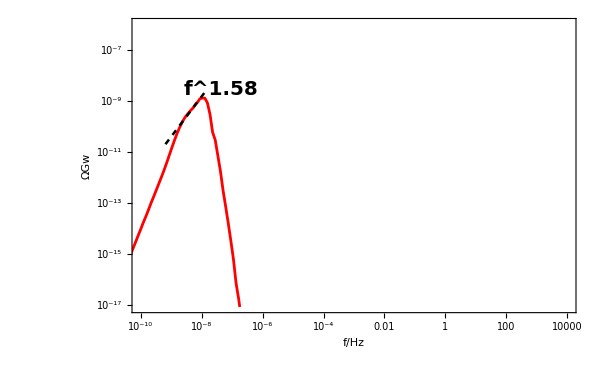

```mathematica
fitD=Show[LogLogPlot[s x^b/.{s->ddA,b->bbA},{x,data[[1,1]]*2,data[[Length[data],1]]*1.8},PlotStyle->{{Dashing[0.007],Black,Thickness[0.003]}}]];
Show[omega,fitD,Epilog->{Text[Style["f^1.58",20,FontFamily->"Cambria",Bold],Scaled[{0.20,.76}]]},ImageSize->{600,400}]
```

```mathematica
data2={{1.563660078749857*^-8,8.047233984100762*^-10},{1.898714233709046*^-8,2.884338644415862*^-10},{2.3081315642267898*^-8,5.699170847031396*^-11},{2.8076936145407367*^-8,2.8777031329630177*^-11},{3.416779229519207*^-8,7.114914163289739*^-12},{4.1590843793217786*^-8,1.7371020743068985*^-12},{5.063418378600366*^-8,3.09878791477221*^-13},{6.164994022532839*^-8,7.180857291671158*^-14},{7.506680749207727*^-8,1.5728013693773118*^-14},{9.140696804241328*^-8,3.1995931846418112*^-15},{1.1130638618913502*^-7,6.002717333246757*^-16}};
```

```mathematica
BB=FindFit[data2,d x^-b,{d,b},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{d→4.06531×10^-23,b→1.67554}

```mathematica
ddB=BB[[1]][[2]];
bbB=BB[[2]][[2]];
```

### observation data

```mathematica
ska=Import["plis_ska.dat"];
lisa=Import["plis_LISA.dat"];
dec=Import["plis_DECIGO.dat"];
bbo=Import["plis_BBO.dat"];
ppta=Import["plis_ppta.dat"];
epta=Import["plis_EPTA.dat"];
ipta=Import["plis_ipta.dat"];

ce=Import["plis_CE.dat"];
et=Import["plis_ET.dat"];
hl=Import["plis_HL.dat"];
ngrl=Import["NGR-Low.dat"];
ngru=Import["NGR-Up.dat"];
```

### Omega BG

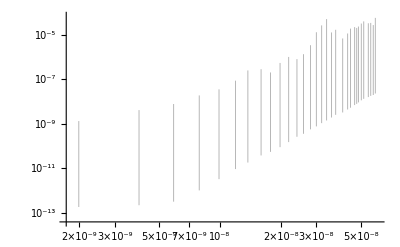

```mathematica
SKA:=Table[{10^(ska[[i,1]]),10^(ska[[i,2]])},{i,Length[ska]}];
LISA:=Table[{10^(lisa[[i,1]]),10^(lisa[[i,2]])},{i,Length[lisa]}];
DEC:=Table[{10^(dec[[i,1]]),10^(dec[[i,2]])},{i,Length[dec]}];
BBO:=Table[{10^(bbo[[i,1]]),10^(bbo[[i,2]])},{i,Length[bbo]}];
PPTA:=Table[{10^(ppta[[i,1]]),10^(ppta[[i,2]])},{i,Length[ppta]}];
EPTA:=Table[{10^(epta[[i,1]]),10^(epta[[i,2]])},{i,Length[epta]}];
IPTA:=Table[{10^(ipta[[i,1]]),10^(ipta[[i,2]])},{i,Length[ipta]}];

CE:=Table[{10^(ce[[i,1]]),10^(ce[[i,2]])},{i,Length[ce]}];
ET:=Table[{10^(et[[i,1]]),10^(et[[i,2]])},{i,Length[et]}];
HL:=Table[{10^(hl[[i,1]]),10^(hl[[i,2]])},{i,Length[hl]}];
(*NGR:=Table[{10^(ngr[[i,1]]),10^(ngr[[i,2]])},{i,Length[ngr]}];*)
NGR=ListLogLogPlot[{ngrl,ngru},Filling->{1->{{2},Directive[Lighter[Gray],Thickness[0.0015]]}},PlotStyle->Directive[PointSize[0.002],Transparent],Joined->False]
```

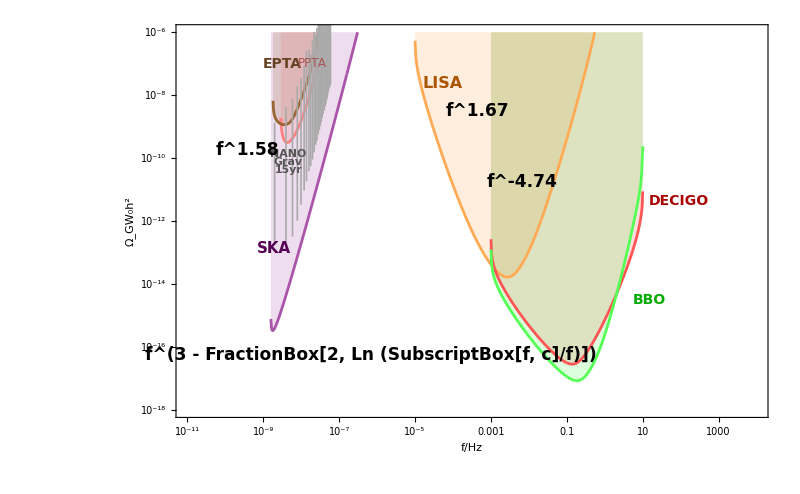

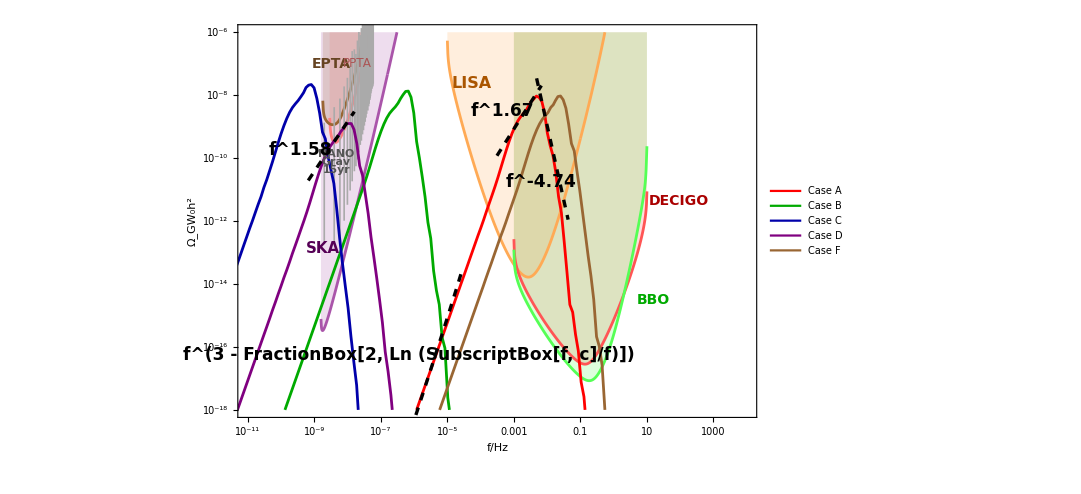

```mathematica
omegabg=ListLogLogPlot[{SKA,LISA,DEC,BBO,PPTA,EPTA},Frame->True,PlotRange->{{10^-11,10^4},{10^-18,10^-6}},FrameLabel->{"f/Hz","Ω_GW_0h^2"},Frame-> True,LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{800,600},Axes->False,Joined->True,Filling->Top,PlotStyle->{Lighter[Purple],Lighter[Orange],Lighter[Red],Lighter[Green],Pink,Brown},Epilog->{Text[Style["SKA",15,FontFamily->"Cambria",Bold,Darker[Purple]],Scaled[{.165,0.43}]],
Text[Style["LISA",16,FontFamily->"Cambria",Bold,Darker[Orange]],Scaled[{0.45,0.85}]],Text[Style["DECIGO",14,FontFamily->"Cambria",Bold,Darker[Red]],Scaled[{0.85,0.55}]],Text[Style["BBO",14,FontFamily->"Cambria",Bold,Darker[Green]],Scaled[{0.8,0.3}]],Text[Style[" ",14,FontFamily->"Cambria",Bold,Darker[Gray]],Scaled[{.10,0.65}]],
Text[Style["EPTA",14,FontFamily->"Cambria",Bold,Darker[Brown]],Scaled[{0.18,0.9}]],
Inset[Style["PPTA",12,FontFamily->"Cambria",Darker[Pink]],Scaled[{.23,0.9}],Automatic,Automatic,{2,3.7}],
Text[Style["f^(3 - FractionBox[2, Ln (SubscriptBox[f, c]/f)])",17,FontFamily->"Cambria",Bold],Scaled[{0.33,0.16}]],
Text[Style["NANO",11,FontFamily->"Courier",Bold,Darker[Gray]],Scaled[{.19,0.67}](*,Automatic*)(*,{1.5,4.5}*)],
Text[Style["Grav",11,FontFamily->"Courier",Bold,Darker[Gray]],Scaled[{.19,0.65}]],
Text[Style["15yr",11,FontFamily->"Courier",Bold,Darker[Gray]],Scaled[{.19,0.63}](*,Automatic*)(*,{1.5,4.5}*)],
Text[Style["f^1.58",17,FontFamily->"Cambria",Bold],Scaled[{0.12,0.68}]],Text[Style["f^1.67",17,FontFamily->"Cambria",Bold],Scaled[{0.51,.78}]],
Text[Style["f^-4.74",17,FontFamily->"Cambria",Bold],Scaled[{0.585,.60}]]}];
omegaBG=Show[(*NGR,*)omegabg,NGR]

oa=Import["GWA.dat"];
ob=Import["GWB.dat"];
oc=Import["GWC.dat"];
od=Import["GWD.dat"];
of=Import["GWF.dat"];
omega=ListLogLogPlot[{oa,ob,oc,od,of},Frame->True,PlotRange->{{10^-11,10^4},{1*10^-18,10^-6}},PlotStyle->{Red,Darker[Green],Darker[Blue],Purple,Brown},FrameLabel->{"f/Hz","ΩGw"},RotateLabel->False,Joined->True,Axes->False,LabelStyle->{FontFamily->"Cambria",Bold,GrayLevel[0]},ImageSize->{600,400},PlotLegends->{Placed[LineLegend[{Red,Darker[Green],Darker[Blue],Purple,Brown},{"Case A","Case B ","Case C","Case D","Case F"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.9,0.78}]}];
omegafinal=Show[omegaBG,omega,fitA,fitB,fitC,fitD]
```

```mathematica
Export["Gw.eps",omegafinal];
```

## Fitting Ω_GW B

```mathematica
SetDirectory[NotebookDirectory[]];
oa=Import["GWB.dat"];
```

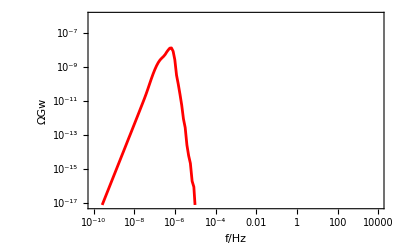

```mathematica
omega=ListLogLogPlot[{oa},Frame->True,PlotRange->{{10^-10,10^4},{8*10^-18,10^-6}},PlotStyle->{Red},FrameLabel->{"f/Hz","ΩGw"},RotateLabel->False,Joined->True,Axes->False,LabelStyle->{FontFamily->"Cambria",Bold,GrayLevel[0]}]
```

```mathematica
oa
```

{{4.41162×10^-14,3.8378×10^-29},{5.37891×10^-14,6.95619×10^-29},{6.55825×10^-14,1.26082×10^-28},{7.99612×10^-14,2.28521×10^-28},{9.74917×10^-14,4.14182×10^-28},{1.18865×10^-13,7.50667×10^-28},{1.44922×10^-13,1.36049×10^-27},{1.76691×10^-13,2.46567×10^-27},{2.15423×10^-13,4.46855×10^-27},{2.62644×10^-13,8.09822×10^-27},{3.20212×10^-13,1.46758×10^-26},{3.90397×10^-13,2.65955×10^-26},{4.75962×10^-13,4.81953×10^-26},{5.80276×10^-13,8.73358×10^-26},{7.07447×10^-13,1.5826×10^-25},{8.62483×10^-13,2.86775×10^-25},{1.05149×10^-12,5.19639×10^-25},{1.2819×10^-12,9.41572×10^-25},{1.5628×10^-12,1.70607×10^-24},{1.90523×10^-12,3.09122×10^-24},{2.32267×10^-12,5.60083×10^-24},{2.83156×10^-12,1.01477×10^-23},{3.45193×10^-12,1.83854×10^-23},{4.20817×10^-12,3.33096×10^-23},{5.13005×10^-12,6.03468×10^-23},{6.25385×10^-12,1.09328×10^-22},{7.62377×10^-12,1.98061×10^-22},{9.2937×10^-12,3.58805×10^-22},{1.13293×10^-11,6.49981×10^-22},{1.38107×10^-11,1.17743×10^-21},{1.68355×10^-11,2.1329×10^-21},{2.05225×10^-11,3.86351×10^-21},{2.50169×10^-11,6.99828×10^-21},{3.04952×10^-11,1.2676×10^-20},{3.7173×10^-11,2.29596×10^-20},{4.53126×10^-11,4.15848×10^-20},{5.52341×10^-11,7.53179×10^-20},{6.73274×10^-11,1.36422×10^-19},{8.20678×10^-11,2.47094×10^-19},{1.00035×10^-10,4.47414×10^-19},{1.21934×10^-10,8.10321×10^-19},{1.48626×10^-10,1.46741×10^-18},{1.81159×10^-10,2.65772×10^-18},{2.20811×10^-10,4.81235×10^-18},{2.69141×10^-10,8.71504×10^-18},{3.28045×10^-10,1.57823×10^-17},{3.99837×10^-10,2.8579×10^-17},{4.87337×10^-10,5.17311×10^-17},{5.9398×10^-10,9.3639×10^-17},{7.23955×10^-10,1.69664×10^-16},{8.82363×10^-10,3.0715×10^-16},{1.07542×10^-9,5.5563×10^-16},{1.31071×10^-9,1.00574×10^-15},{1.59746×10^-9,1.82397×10^-15},{1.94692×10^-9,3.29644×10^-15},{2.37281×10^-9,5.98858×10^-15},{2.89183×10^-9,1.07863×10^-14},{3.52434×10^-9,1.95539×10^-14},{4.29514×10^-9,3.55593×10^-14},{5.23447×10^-9,6.47312×10^-14},{6.37913×10^-9,1.16051×10^-13},{7.77401×10^-9,2.10605×10^-13},{9.47376×10^-9,3.81755×10^-13},{1.1545×10^-8,6.9282×10^-13},{1.40688×10^-8,1.25726×10^-12},{1.71441×10^-8,2.28732×10^-12},{2.08911×10^-8,4.1744×10^-12},{2.54566×10^-8,7.60661×10^-12},{3.1019×10^-8,1.39231×10^-11},{3.77959×10^-8,2.62809×10^-11},{4.60518×10^-8,5.15336×10^-11},{5.61088×10^-8,1.03508×10^-10},{6.83584×10^-8,2.06144×10^-10},{8.32767×10^-8,3.95186×10^-10},{1.01442×10^-7,7.16001×10^-10},{1.23556×10^-7,1.20903×10^-9},{1.50469×10^-7,1.87516×10^-9},{1.83203×10^-7,2.6455×10^-9},{2.22983×10^-7,3.39818×10^-9},{2.71232×10^-7,4.24031×10^-9},{3.29451×10^-7,5.59445×10^-9},{3.93177×10^-7,7.84811×10^-9},{4.64844×10^-7,1.02941×10^-8},{5.55307×10^-7,1.3151×10^-8},{6.6817×10^-7,1.35029×10^-8},{8.07641×10^-7,8.62487×10^-9},{9.78933×10^-7,2.71583×10^-9},{1.18855×10^-6,3.36853×10^-10},{1.4445×10^-6,1.00594×10^-10},{1.75664×10^-6,2.5549×10^-11},{2.13701×10^-6,5.84837×10^-12},{2.60032×10^-6,9.11751×10^-13},{3.16454×10^-6,2.81986×10^-13},{3.8515×10^-6,2.65072×10^-14},{4.6878×10^-6,6.23903×10^-15},{5.70583×10^-6,2.22683×10^-15},{6.94504×10^-6,2.00271×10^-16},{8.4534×10^-6,9.14409×10^-17},{0.0000102894,2.45354×10^-18},{0.0000125239,5.18141×10^-19},{0.0000152435,7.10152×10^-19},{0.0000185534,7.37847×10^-20},{0.0000225816,2.19238×10^-20},{0.0000274837,1.60903×10^-21},{0.0000334492,4.072×10^-23},{0.0000407087,1.04213×10^-23},{0.0000495424,3.02082×10^-24},{0.0000602914,1.30561×10^-24},{0.0000733707,5.95735×10^-25}}

```mathematica
ScientificForm[6.681699571628819*^-7]
(*peak={6.681699571628819*^-7,1.3502947288273252*^-8};*)
```

9.92226×10^-7

```mathematica
fc1=6.681699571628819*^-7;
```

```mathematica
data3={{2.6914059509143176*^-10,8.715039383518973*^-18},{3.2804489384208195*^-10,1.5782293468430343*^-17},{3.9983735593251363*^-10,2.8579026576674983*^-17},{4.873370454454881*^-10,5.1731051702082146*^-17},{5.939802274051574*^-10,9.363902413105616*^-17},{7.239553952408371*^-10,1.696638249625491*^-16},{8.823630687703748*^-10,3.0715013767150077*^-16},{1.0754213357070835*^-9,5.556302796448196*^-16},{1.310709170535481*^-9,1.0057387643104467*^-15},{1.5974592603051945*^-9,1.8239692442672157*^-15},{1.9469227499007112*^-9,3.296437436290201*^-15},{2.3728106519645453*^-9,5.988583135075026*^-15},{2.891830785949233*^-9,1.0786260847115817*^-14},{3.5243404539829425*^-9,1.9553876017293976*^-14},{4.2951439804519554*^-9,3.5559318698414675*^-14},{5.234465700369612*^-9,6.473119988337158*^-14},{6.3791316568450505*^-9,1.1605131754381688*^-13},{7.77401022681823*^-9,2.1060493249685063*^-13},{9.473763546044963*^-9,3.8175534983396916*^-13},{1.1544989507336387*^-8,6.928201059605764*^-13},{1.4068820925246275*^-8,1.2572552604728753*^-12},{1.71440716777057*^-8,2.2873180560008574*^-12},{2.0891121188303157*^-8,4.174395824250003*^-12},{2.545659316140165*^-8,7.606614035226204*^-12},{3.1019046283964344*^-8,1.3923066166740536*^-11},{3.779592140000832*^-8,2.6280889739646743*^-11},{4.605184221705054*^-8,5.1533619515511796*^-11},{5.61087808954447*^-8,1.0350817149838043*^-10},{6.83583617839647*^-8,2.0614426319775982*^-10},{8.327665927220977*^-8,3.9518599511998084*^-10},{1.0144201580765565*^-7,7.160007545338343*^-10},{1.235562728171516*^-7,1.209031782675643*^-9},{1.5046908334727457*^-7,1.8751566827413155*^-9},{1.8320282945299837*^-7,2.645496497160346*^-9},{2.2298278508253269*^-7,3.3981790162290574*^-9}};
```

```mathematica
CC=FindFit[data3,x^(d-2/Log[fc1/x]),{d,b},x]
```

{d→3.09503,b→1.}

```mathematica
ddC=CC[[1]][[2]]
bbC=CC[[2]][[2]]
```

3.09503

1.

```mathematica
data={{7.77401022681823*^-9,2.1060493249685063*^-13},{9.473763546044963*^-9,3.8175534983396916*^-13},{1.1544989507336387*^-8,6.928201059605764*^-13},{1.4068820925246275*^-8,1.2572552604728753*^-12},{1.71440716777057*^-8,2.2873180560008574*^-12},{2.0891121188303157*^-8,4.174395824250003*^-12},{2.545659316140165*^-8,7.606614035226204*^-12},{3.1019046283964344*^-8,1.3923066166740536*^-11},{3.779592140000832*^-8,2.6280889739646743*^-11},{4.605184221705054*^-8,5.1533619515511796*^-11},{5.61087808954447*^-8,1.0350817149838043*^-10},{6.83583617839647*^-8,2.0614426319775982*^-10},{8.327665927220977*^-8,3.9518599511998084*^-10},{1.0144201580765565*^-7,7.160007545338343*^-10},{1.235562728171516*^-7,1.209031782675643*^-9},{1.5046908334727457*^-7,1.8751566827413155*^-9},{1.8320282945299837*^-7,2.645496497160346*^-9},{2.2298278508253269*^-7,3.3981790162290574*^-9},{2.712317696093648*^-7,4.240311561804648*^-9},{3.294508475908454*^-7,5.594451117753124*^-9},{3.9317663526937294*^-7,7.848111211315385*^-9},{4.6484385287050584*^-7,1.0294148769470786*^-8},{5.553065575998761*^-7,1.3150999511904057*^-8}};
```

```mathematica
AA=FindFit[data,s x^b,{s,b},x]
```

{s→95.6004,b→1.57555}

```mathematica
{b,s}/.AA
```

{1.57555,95.6004}

```mathematica
ddA=AA[[1]][[2]]
bbA=AA[[2]][[2]]
```

95.6004

1.57555

```mathematica
data2={{8.076407535209682*^-7,8.624865939991726*^-9},{9.789327863486385*^-7,2.715833771188429*^-9},{1.1885479299261224*^-6,3.368525933213844*^-10},{1.4444999455042078*^-6,1.0059359931242845*^-10},{1.7566365622566706*^-6,2.5548990506942427*^-11},{2.1370056581025672*^-6,5.848367460091797*^-12},{2.6003247979865143*^-6,9.117505082902146*^-13},{3.1645404863352176*^-6,2.8198587681776795*^-13},{3.8514995738397175*^-6,2.6507182190080082*^-14},{4.687799601936185*^-6,6.23903135016542*^-15},{5.705831323998104*^-6,2.2268335964260855*^-15},{6.945044154816923*^-6,2.0027086269390304*^-16}};
```

```mathematica
BB=FindFit[data2,d x^-b,{d,b},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{d→4.30864×10^-19,b→1.65235}

```mathematica
ddB=BB[[1]][[2]];
bbB=BB[[2]][[2]];
```

## Fitting Ω_GW C

```mathematica
SetDirectory[NotebookDirectory[]];
oa=Import["GWC.dat"];
```

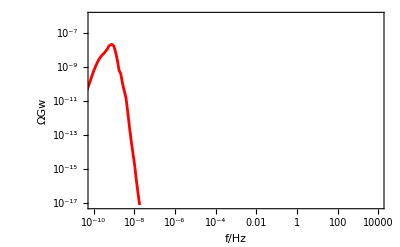

```mathematica
omega=ListLogLogPlot[{oa},Frame->True,PlotRange->{{10^-10,10^4},{8*10^-18,10^-6}},PlotStyle->{Red},FrameLabel->{"f/Hz","ΩGw"},RotateLabel->False,Joined->True,Axes->False,LabelStyle->{FontFamily->"Cambria",Bold,GrayLevel[0]}]
```

```mathematica
oa
```

{{9.42671×10^-17,3.24116×10^-28},{1.14958×10^-16,5.87809×10^-28},{1.40189×10^-16,1.06602×10^-27},{1.70958×10^-16,1.93324×10^-27},{2.08478×10^-16,3.50592×10^-27},{2.54232×10^-16,6.35786×10^-27},{3.10026×10^-16,1.15296×10^-26},{3.78062×10^-16,2.09078×10^-26},{4.61026×10^-16,3.79138×10^-26},{5.62194×10^-16,6.8751×10^-26},{6.85559×10^-16,1.24668×10^-25},{8.35989×10^-16,2.26059×10^-25},{1.01942×10^-15,4.09905×10^-25},{1.2431×10^-15,7.43253×10^-25},{1.51584×10^-15,1.34767×10^-24},{1.84842×10^-15,2.44357×10^-24},{2.25396×10^-15,4.43055×10^-24},{2.74845×10^-15,8.03307×10^-24},{3.35141×10^-15,1.45647×10^-23},{4.08662×10^-15,2.64065×10^-23},{4.98309×10^-15,4.78758×10^-23},{6.07618×10^-15,8.67988×10^-23},{7.40902×10^-15,1.57365×10^-22},{9.03416×10^-15,2.85288×10^-22},{1.10157×10^-14,5.17197×10^-22},{1.34318×10^-14,9.37618×10^-22},{1.63778×10^-14,1.69973×10^-21},{1.99697×10^-14,3.08125×10^-21},{2.43493×10^-14,5.58561×10^-21},{2.96891×10^-14,1.01249×10^-20},{3.61999×10^-14,1.83548×10^-20},{4.41381×10^-14,3.32676×10^-20},{5.38167×10^-14,6.03137×10^-20},{6.56173×10^-14,1.09314×10^-19},{8.00049×10^-14,1.98133×10^-19},{9.75467×10^-14,3.59183×10^-19},{1.18934×10^-13,6.50937×10^-19},{1.45009×10^-13,1.17997×10^-18},{1.768×10^-13,2.13906×10^-18},{2.1556×10^-13,3.87433×10^-18},{2.62814×10^-13,7.02347×10^-18},{3.20426×10^-13,1.27318×10^-17},{3.90664×10^-13,2.30719×10^-17},{4.76295×10^-13,4.17719×10^-17},{5.80692×10^-13,7.57435×10^-17},{7.07967×10^-13,1.37248×10^-16},{8.63131×10^-13,2.48825×10^-16},{1.05229×10^-12,4.50604×10^-16},{1.28291×10^-12,8.16507×10^-16},{1.56404×10^-12,1.48394×10^-15},{1.90678×10^-12,2.68269×10^-15},{2.32459×10^-12,4.84277×10^-15},{2.83394×10^-12,8.81227×10^-15},{3.45487×10^-12,1.59929×10^-14},{4.2118×10^-12,2.90607×10^-14},{5.13452×10^-12,5.2552×10^-14},{6.25933×10^-12,9.54584×10^-14},{7.63048×10^-12,1.74789×10^-13},{9.30188×10^-12,3.16995×10^-13},{1.13393×10^-11,5.79276×10^-13},{1.38227×10^-11,1.02511×10^-12},{1.68498×10^-11,1.87675×10^-12},{2.05396×10^-11,3.41158×10^-12},{2.5037×10^-11,5.97584×10^-12},{3.05185×10^-11,1.17404×10^-11},{3.71992×10^-11,2.07398×10^-11},{4.53411×10^-11,3.97881×10^-11},{5.52632×10^-11,7.65343×10^-11},{6.73539×10^-11,1.53742×10^-10},{8.20861×10^-11,3.08853×10^-10},{1.00034×10^-10,5.9387×10^-10},{1.21897×10^-10,1.07526×10^-9},{1.48522×10^-10,1.82263×10^-9},{1.80936×10^-10,2.85375×10^-9},{2.20378×10^-10,4.06015×10^-9},{2.68331×10^-10,5.30413×10^-9},{3.26533×10^-10,6.75241×10^-9},{3.96829×10^-10,9.0316×10^-9},{4.74496×10^-10,1.19918×10^-8},{5.62704×10^-10,1.7526×10^-8},{6.73691×10^-10,2.084×10^-8},{8.11885×10^-10,2.18024×10^-8},{9.82474×10^-10,1.71408×10^-8},{1.19192×10^-9,7.85513×10^-9},{1.44821×10^-9,2.68132×10^-9},{1.76124×10^-9,6.68593×10^-10},{2.14314×10^-9,4.10622×10^-10},{2.60875×10^-9,1.11507×10^-10},{3.17618×10^-9,4.14519×10^-11},{3.86758×10^-9,1.57613×10^-11},{4.70989×10^-9,2.44489×10^-12},{5.73593×10^-9,3.04865×10^-13},{6.98572×10^-9,4.71786×10^-14},{8.50798×10^-9,8.80939×10^-15},{1.03621×10^-8,1.72145×10^-15},{1.26203×10^-8,2.16586×10^-16},{1.53706×10^-8,3.43213×10^-17},{1.87202×10^-8,6.06115×10^-18},{2.27996×10^-8,2.36305×10^-19},{2.77676×10^-8,4.81594×10^-20},{3.38177×10^-8,3.71782×10^-20},{4.11854×10^-8,4.48867×10^-21},{5.01577×10^-8,5.38353×10^-22},{6.10838×10^-8,7.38671×10^-23},{7.43889×10^-8,3.04434×10^-23},{9.05905×10^-8,1.37826×10^-23},{1.10319×10^-7,6.15704×10^-24},{1.34342×10^-7,2.70437×10^-24},{1.63592×10^-7,1.26172×10^-24},{1.99208×10^-7,5.5055×10^-25},{2.42574×10^-7,2.53123×10^-25},{2.95374×10^-7,1.10899×10^-25},{3.59661×10^-7,5.02245×10^-26},{4.37932×10^-7,2.27466×10^-26},{5.33225×10^-7,1.01931×10^-26},{6.49243×10^-7,4.56073×10^-27},{7.90487×10^-7,2.05797×10^-27},{9.62439×10^-7,9.21582×10^-28},{1.17177×10^-6,4.15893×10^-28},{1.42661×10^-6,1.85565×10^-28},{1.73683×10^-6,8.40922×10^-29},{2.11446×10^-6,3.74573×10^-29},{2.57415×10^-6,1.69402×10^-29},{3.1337×10^-6,7.57041×10^-30},{3.8148×10^-6,3.419×10^-30},{4.64384×10^-6,1.53347×10^-30},{5.65292×10^-6,6.88574×10^-31},{6.8811×10^-6,3.09458×10^-31},{8.37593×10^-6,1.39266×10^-31},{0.0000101953,6.25566×10^-32},{0.0000124095,2.81014×10^-32},{0.0000151042,1.26347×10^-32},{0.0000183836,5.67982×10^-33},{0.0000223745,2.55165×10^-33},{0.0000272312,1.1459×10^-33},{0.0000331411,5.15666×10^-34},{0.0000403326,2.31586×10^-34},{0.0000490833,1.04236×10^-34},{0.0000597311,4.69453×10^-35},{0.0000726867,2.16305×10^-35},{0.0000884499,1.04541×10^-35},{0.000107629,5.28013×10^-36},{0.000130962,3.71246×10^-36},{0.00015935,3.68735×10^-36},{0.000193885,5.21273×10^-36},{0.000235898,6.82416×10^-36},{0.000287006,9.60866×10^-36},{0.000349176,1.23525×10^-35},{0.0004248,1.96573×10^-35},{0.000516786,2.97536×10^-35},{0.00062867,4.40175×10^-35},{0.000764753,5.94322×10^-35},{0.000930262,8.30948×10^-35},{0.00113155,1.11065×10^-34},{0.00137635,1.64845×10^-34},{0.00167405,2.37689×10^-34},{0.00203607,3.60372×10^-34},{0.00247628,6.01715×10^-34},{0.00301156,7.03077×10^-34},{0.00366242,1.19399×10^-33},{0.00445377,1.73178×10^-33},{0.00541591,2.50132×10^-33},{0.00658563,3.57467×10^-33},{0.00800766,5.17318×10^-33},{0.00973636,7.69006×10^-33},{0.0118378,1.07206×10^-32},{0.0143921,1.46998×10^-32},{0.0174969,1.87898×10^-32},{0.0212705,3.08089×10^-32},{0.0258568,5.71186×10^-32},{0.0314307,6.88622×10^-32},{0.0382042,9.73548×10^-32},{0.0464354,1.56315×10^-31},{0.0564372,1.76926×10^-31},{0.06859,3.23476×10^-31},{0.0833555,5.01603×10^-31},{0.101294,6.74466×10^-31},{0.123088,1.03402×10^-30},{0.149562,1.40148×10^-30},{0.18172,1.75381×10^-30},{0.220781,2.61256×10^-30},{0.268222,4.29977×10^-30},{0.325839,6.31799×10^-30},{0.395809,8.42857×10^-30},{0.480776,1.49409×10^-29},{0.583946,1.7519×10^-29},{0.709211,2.23854×10^-29},{0.861291,3.69644×10^-29},{1.04592,5.4863×10^-29},{1.27003,7.64082×10^-29},{1.54206,1.22795×10^-28},{1.87222,1.54246×10^-28},{2.27291,2.12568×10^-28},{2.75915,2.98635×10^-28},{3.34916,5.40791×10^-28},{4.06501,7.67825×10^-28},{4.93348,1.03745×10^-27},{5.987,1.44723×10^-27},{7.26489,2.15189×10^-27},{8.81478,2.7999×10^-27},{10.6944,4.2553×10^-27},{12.9736,5.89973×10^-27},{15.737,8.48694×10^-27},{19.0873,1.38685×10^-26},{23.1486,1.40126×10^-26},{28.0711,2.45745×10^-26},{34.0368,3.68924×10^-26},{41.2659,4.95233×10^-26},{50.0249,6.87745×10^-26},{60.6361,1.11098×10^-25},{73.4896,1.57751×10^-25},{89.057,2.09213×10^-25},{107.909,2.9561×10^-25},{130.734,4.30017×10^-25},{158.366,5.85572×10^-25}}

```mathematica
ScientificForm[8.118848655871785*^-10]
(*peak={8.118848655871785*^-10,2.1802355214318777*^-8};*)
```

8.11885×10^-10

```mathematica
fc1=8.118848655871785*^-10;
```

```mathematica
data3={ {3.2042599811196953*^-13,1.2731792870525975*^-17},{3.9066411633967226*^-13,2.307185396882075*^-17},{4.762953708629579*^-13,4.177188450401596*^-17},{5.806924563693414*^-13,7.574347542006714*^-17},{7.079668647441581*^-13,1.3724808576644958*^-16},{8.631307376674399*^-13,2.488252104670279*^-16},{1.0522940570124542*^-12,4.506044679845217*^-16},{1.2829050332930155*^-12,8.165066502058822*^-16},{1.5640429899798194*^-12,1.4839406670203559*^-15},{1.906775672153592*^-12,2.6826930194368015*^-15},{2.324594563848314*^-12,4.8427719309732446*^-15},{2.83394360009934*^-12,8.812266059854057*^-15},{3.454866372906571*^-12,1.5992864316645588*^-14},{4.211796674083889*^-12,2.906066802898489*^-14},{5.134517449456964*^-12,5.255198217692993*^-14},{6.259329169511148*^-12,9.545841132011909*^-14},{7.630477025008388*^-12,1.7478913691235061*^-13},{9.301881063280344*^-12,3.1699517538543477*^-13},{1.133926379694329*^-11,5.792755793408076*^-13},{1.3822715730506989*^-11,1.0251073867831288*^-12},{1.6849836673316673*^-11,1.8767537082996364*^-12},{2.0539599112686345*^-11,3.4115843727175667*^-12},{2.503696492273519*^-11,5.97584477361716*^-12},{3.0518503042545715*^-11,1.1740418378295432*^-11},{3.719922857724193*^-11,2.073984406022983*^-11},{4.5341114472675596*^-11,3.9788111357534804*^-11},{5.526321238283022*^-11,7.653431724908966*^-11},{6.735394881172674*^-11,1.537417304823225*^-10},{8.208607590066287*^-11,3.088525559757408*^-10},{1.0003416559807545*^-10,5.938697440440049*^-10},{1.2189661706144584*^-10,1.0752567261792868*^-9},{1.4852170242493714*^-10,1.822626632482262*^-9},{1.8093589882173985*^-10,2.853752926600915*^-9},{2.2037813045759216*^-10,4.060147505730554*^-9},{2.6833114042034284*^-10,5.304134817151151*^-9},{3.2653297859754515*^-10,6.7524081577598434*^-9}};
```

```mathematica
CC=FindFit[data3, x^(d-2/Log[fc1/x]),{d,b},x]
```

{d→3.05712,b→1.}

```mathematica
ddC=CC[[1]][[2]]
bbC=CC[[2]][[2]]
```

3.05712

1.

```mathematica
data={{1.3822715730506989*^-11,1.0251073867831288*^-12},{1.6849836673316673*^-11,1.8767537082996364*^-12},{2.0539599112686345*^-11,3.4115843727175667*^-12},{2.503696492273519*^-11,5.97584477361716*^-12},{3.0518503042545715*^-11,1.1740418378295432*^-11},{3.719922857724193*^-11,2.073984406022983*^-11},{4.5341114472675596*^-11,3.9788111357534804*^-11},{5.526321238283022*^-11,7.653431724908966*^-11},{6.735394881172674*^-11,1.537417304823225*^-10},{8.208607590066287*^-11,3.088525559757408*^-10},{1.0003416559807545*^-10,5.938697440440049*^-10},{1.2189661706144584*^-10,1.0752567261792868*^-9},{1.4852170242493714*^-10,1.822626632482262*^-9},{1.8093589882173985*^-10,2.853752926600915*^-9},{2.2037813045759216*^-10,4.060147505730554*^-9},{2.6833114042034284*^-10,5.304134817151151*^-9},{3.2653297859754515*^-10,6.7524081577598434*^-9},{3.968293449761045*^-10,9.031599743475871*^-9},{4.744961327439054*^-10,1.1991791618023968*^-8},{5.627041517206549*^-10,1.752597068285978*^-8}(*,{6.736910491658488*^-10,2.084001509567095*^-8}*)};
```

```mathematica
AA=FindFit[data,s x^b,{s,b},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{s→4.61758×10^7,b→1.66894}

```mathematica
{b,s}/.AA
```

{1.66894,4.61758×10^7}

```mathematica
ddA=AA[[1]][[2]]
bbA=AA[[2]][[2]]
```

4.61758×10^7

1.66894

```mathematica
data2={{1.1919164706384928*^-9,7.85512889526513*^-9},{1.4482135010041296*^-9,2.6813215985619607*^-9},{1.7612426685348077*^-9,6.685933407821435*^-10},{2.143142730107257*^-9,4.1062222145197757*^-10},{2.608745550983397*^-9,1.1150728345423539*^-10},{3.176183028566678*^-9,4.145192034840658*^-11},{3.867584897789766*^-9,1.576126643681502*^-11},{4.709885103707402*^-9,2.4448854707247238*^-12},{5.735925966585795*^-9,3.048653756943121*^-13},{6.9857152800328434*^-9,4.71785622177947*^-14},{8.50798447721961*^-9,8.809386831585507*^-15},{1.0362082866020987*^-8,1.7214507100091988*^-15},{1.2620284785646118*^-8,2.1658572639319466*^-16}};
```

```mathematica
BB=FindFit[data2,d x^-b,{d,b},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{d→3.54594×10^-25,b→1.8112}

```mathematica
ddB=BB[[1]][[2]];
bbB=BB[[2]][[2]];
```

## Fitting Ω_GW F

```mathematica
SetDirectory[NotebookDirectory[]];
oa=Import["GWF.dat"];
```

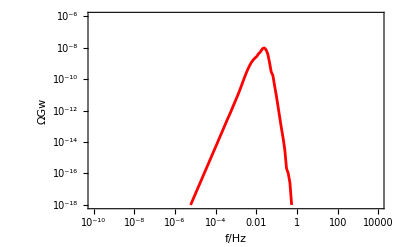

```mathematica
omega=ListLogLogPlot[{oa},Frame->True,PlotRange->{{10^-10,10^4},{10^-18,10^-6}},PlotStyle->{Red},FrameLabel->{"f/Hz","ΩGw"},RotateLabel->False,Joined->True,Axes->False,LabelStyle->{FontFamily->"Cambria",Bold,GrayLevel[0]}]
```

```mathematica
oa
```

{{5.10459×10^-9,6.61668×10^-28},{6.21843×10^-9,1.19619×10^-27},{7.57523×10^-9,2.16245×10^-27},{9.22792×10^-9,3.90905×10^-27},{1.1241×10^-8,7.06606×10^-27},{1.36931×10^-8,1.27722×10^-26},{1.66798×10^-8,2.30853×10^-26},{2.03177×10^-8,4.17239×10^-26},{2.47487×10^-8,7.54077×10^-26},{3.01455×10^-8,1.36279×10^-25},{3.67186×10^-8,2.46275×10^-25},{4.47243×10^-8,4.45031×10^-25},{5.44746×10^-8,8.04157×10^-25},{6.63495×10^-8,1.45302×10^-24},{8.08118×10^-8,2.62532×10^-24},{9.84248×10^-8,4.74321×10^-24},{1.19875×10^-7,8.56924×10^-24},{1.45997×10^-7,1.54807×10^-23},{1.77808×10^-7,2.79649×10^-23},{2.16547×10^-7,5.05145×10^-23},{2.63722×10^-7,9.12424×10^-23},{3.21168×10^-7,1.648×10^-22},{3.91121×10^-7,2.97647×10^-22},{4.76302×10^-7,5.37531×10^-22},{5.80024×10^-7,9.70705×10^-22},{7.06321×10^-7,1.7529×10^-21},{8.60102×10^-7,3.16518×10^-21},{1.04734×10^-6,5.71505×10^-21},{1.27533×10^-6,1.03182×10^-20},{1.5529×10^-6,1.86275×10^-20},{1.89086×10^-6,3.36293×10^-20},{2.30232×10^-6,6.07096×10^-20},{2.80327×10^-6,1.09585×10^-19},{3.41314×10^-6,1.97813×10^-19},{4.15561×10^-6,3.56957×10^-19},{5.05949×10^-6,6.44245×10^-19},{6.15985×10^-6,1.16274×10^-18},{7.49936×10^-6,2.0986×10^-18},{9.12996×10^-6,3.78588×10^-18},{0.0000111149,6.83472×10^-18},{0.000013531,1.23203×10^-17},{0.000016472,2.22388×10^-17},{0.0000200517,4.01406×10^-17},{0.0000244089,7.24368×10^-17},{0.0000297122,1.30565×10^-16},{0.0000361668,2.35367×10^-16},{0.0000440227,4.24469×10^-16},{0.0000535836,7.65789×10^-16},{0.0000652194,1.37757×10^-15},{0.0000793803,2.49444×10^-15},{0.0000966134,4.48842×10^-15},{0.000117585,8.04829×10^-15},{0.000143104,1.47227×10^-14},{0.000174158,2.65988×10^-14},{0.000211945,4.73998×10^-14},{0.000257924,8.66215×10^-14},{0.000313867,1.56775×10^-13},{0.000381933,2.85309×10^-13},{0.000464746,4.92593×10^-13},{0.000565496,8.79642×10^-13},{0.000688066,1.62886×10^-12},{0.000837175,2.94953×10^-12},{0.00101856,5.35635×10^-12},{0.0012392,9.80953×10^-12},{0.00150758,1.85719×10^-11},{0.00183398,3.6791×10^-11},{0.00223094,7.27661×10^-11},{0.00271363,1.43237×10^-10},{0.00330051,2.70698×10^-10},{0.00401394,4.82908×10^-10},{0.00488087,8.04141×10^-10},{0.00593393,1.23566×10^-9},{0.00721229,1.7296×10^-9},{0.00876211,2.22495×10^-9},{0.0106367,2.82187×10^-9},{0.0128871,4.10875×10^-9},{0.0152191,4.92609×10^-9},{0.0178008,6.78376×10^-9},{0.0210955,9.0689×10^-9},{0.0252301,9.42293×10^-9},{0.0303514,7.15603×10^-9},{0.0366422,3.8559×10^-9},{0.0443311,1.19105×10^-9},{0.0537024,2.90625×10^-10},{0.0651002,1.70017×10^-10},{0.0789496,3.80348×10^-11},{0.0957662,9.34663×10^-12},{0.116175,1.89856×10^-12},{0.140936,3.84629×10^-13},{0.170971,7.69513×10^-14},{0.207397,1.80384×10^-14},{0.251568,3.18507×10^-15},{0.305123,2.11979×10^-16},{0.370047,1.03658×10^-16},{0.448742,2.602×10^-17},{0.544118,1.02316×10^-18},{0.659698,3.41383×10^-20},{0.799744,1.69348×10^-19},{0.969414,1.05902×10^-20}}

```mathematica
ScientificForm[0.025230140590578723]
(*peak={0.025230140590578723,9.422928849820668*^-9};*)
```

2.52301×10^-2

```mathematica
fc1=0.025230140590578723;
```

```mathematica
data3={{6.1598495711707485*^-6,1.1627429992670821*^-18},{7.4993569628498376*^-6,2.0985966448075655*^-18},{9.129955894171797*^-6,3.785883582898387*^-18},{0.000011114858463529625,6.8347207956614884*^-18},{0.000013530992905249414,1.2320301388286336*^-17},{0.00001647197728821474,2.223881331092791*^-17},{0.000020051737333246574,4.014064399137353*^-17},{0.00002440890773108943,7.24368274775953*^-17},{0.000029712186471675103,1.3056526424308543*^-16},{0.00003616684832925911,2.35366518336841*^-16},{0.000044022668189804336,4.2446864245001765*^-16},{0.000053583559061435524,7.657890695345131*^-16},{0.00006521938604525537,1.3775738505952302*^-15},{0.00007938027254157121,2.494440436758699*^-15},{0.00009661337722562407,4.488419954667504*^-15},{0.00011758464427594762,8.048289464198239*^-15}};
```

```mathematica
CC=FindFit[data3, .0002 x^(d-2/Log[fc1/x]),{d,b},x]
```

{d→3.01542,b→1.}

```mathematica
ddC=CC[[1]][[2]]
bbC=CC[[2]][[2]]
```

3.01542

1.

```mathematica
data={{0.0003819331250419007,2.853091286785949*^-13},{0.0004647458631322196,4.925927653356737*^-13},{0.0005654962631826493,8.796416537371405*^-13},{0.000688065856468136,1.6288646594932837*^-12},{0.0008371745717954093,2.9495346830435892*^-12},{0.0010185607747891466,5.356345731183715*^-12},{0.001239202423019558,9.809530588389365*^-12},{0.0015075774429388002,1.857191695964831*^-11},{0.0018339827760649838,3.679096437124035*^-11},{0.0022309377351647903,7.276609944762366*^-11},{0.002713632602125788,1.432365414389783*^-10},{0.003300512901165434,2.7069814517155934*^-10},{0.00401393904622226,4.829084070638658*^-10},{0.004880873032650085,8.041414068998945*^-10},{0.005933933317741964,1.2356581010964216*^-9},{0.00721228760593704,1.7296025829836242*^-9},{0.008762110466104665,2.2249538752886085*^-9},{0.010636653958751293,2.82186944753213*^-9},{0.012887142442268075,4.108747689673944*^-9},{0.015219099210869877,4.926094052443032*^-9}};
```

```mathematica
AA=FindFit[data,s x^b,{s,b},x]
```

{s→4.17838×10^-6,b→1.60245}

```mathematica
{b,s}/.AA
```

{1.60245,4.17838×10^-6}

```mathematica
ddA=AA[[1]][[2]]
bbA=AA[[2]][[2]]
```

4.17838×10^-6

1.60245

```mathematica
data2={{0.04433107781703595,1.1910483104885046*^-9},{0.05370239323765465,2.9062476963977983*^-10},{0.06510024031885223,1.7001743768595026*^-10},{0.07894955343534114,3.80347852941111*^-11},{0.09576621773911392,9.34663243058135*^-12},{0.11617513816020618,1.8985571529979395*^-12},{0.14093613257596066,3.84628756476355*^-13},{0.1709708912978642,7.695126607008755*^-14},{0.20739683021798835,1.80383538379735*^-14},{0.25156792256843047,3.1850682719677597*^-15},{0.30512332839353856,2.1197913764611339*^-16},{0.37004661263227434,1.0365778861934599*^-16}};
```

```mathematica
BB=FindFit[data2,d x^-b,{d,b},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{d→1.52285×10^-18,b→6.5698}

```mathematica
ddB=BB[[1]][[2]];
bbB=BB[[2]][[2]];
```